```mathematica
Zeta[-(1000.I+1)]
```

-1575.36018680522-1109.53796564106 ⅈ

```mathematica
Zeta[-(1000.I)]
```

-8.46309098852087-8.34334485626739 ⅈ

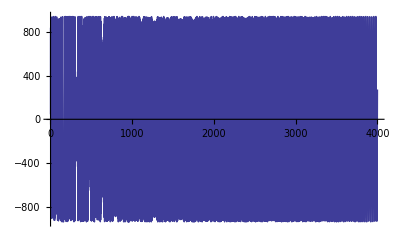

```mathematica
DiscretePlot[Re[1+Zeta[1-1000I]/(-(ⅈ n^(1000 ⅈ))/1000)],{n,1,4000}]
```

```mathematica
Integrate[j^(-1+1000I),{j,0,n}]
```

-(ⅈ n^(1000 ⅈ))/1000

```mathematica
Integrate[j^(1+1000I),{j,0,n}]
```

(1/500002-(250 ⅈ)/250001) n^(2+1000 ⅈ)

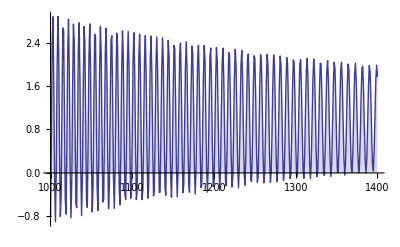

```mathematica
DiscretePlot[Re[1+Zeta[-1-1000I]/((1/500002-(250 ⅈ)/250001) n^(2+1000 ⅈ))],{n,1000,1400}]
```

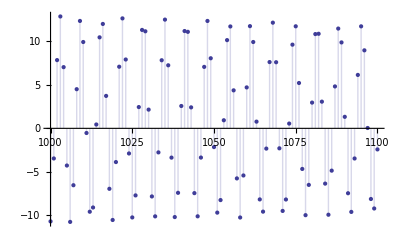

```mathematica
DiscretePlot[Re[1+Zeta[-1000I]/((1/1000001-(1000 ⅈ)/1000001) n^(1+1000 ⅈ))],{n,1000,1100}]
```

```mathematica
Integrate[j^(1000I),{j,0,n}]
```

(1/1000001-(1000 ⅈ)/1000001) n^(1+1000 ⅈ)

```mathematica
Integrate[j^(-1+1000I),{j,0,n}]
```

-(ⅈ n^(1000 ⅈ))/1000

```mathematica
1+Zeta[-1-1000I]/((1/500002-(250 ⅈ)/250001) n^(2+1000 ⅈ))
```

1+(2+1000 ⅈ) n^(-2-1000 ⅈ) Zeta[-1-1000 ⅈ]

```mathematica
Limit[1+Zeta[1-1000 ⅈ]/(-(ⅈ n^(1000 ⅈ))/1000),n->Infinity]
```

1+1000 ⅈ ⅇ^(2 ⅈ Interval[{0,π}]) Zeta[1-1000 ⅈ]

```mathematica
Integrate[j^(s+ t I),{j,0,n}]
```

```mathematica
ConditionalExpression[n^(1+s+ⅈ t)/(1+s+ⅈ t),1+Re[s]>Im[t]]^-1
```

ConditionalExpression[n^(-1-s-ⅈ t) (1+s+ⅈ t),1+Re[s]>Im[t]]

```mathematica
Integrate[j^(s- t I),{j,0,n}]^-1
```

ConditionalExpression[n^(-1-s+ⅈ t) (1+s-ⅈ t),Im[t]+Re[s]>-1]

```mathematica
N[j^(s+t I)-j^(s-t I)/.j->7/.s->3/.t->4]
```

0.+684.304 ⅈ

```mathematica
N[j^s(j^(+t I)-j^(-t I))/.j->7/.s->3/.t->4]
```

0.+684.304 ⅈ

```mathematica
N[j^s(E^(t Log[j] I)-E^(-t Log[j] I))/.j->7/.s->3/.t->4]
```

0.+684.304 ⅈ

```mathematica
N[j^s 2 I Sin[t Log[j]] /. j -> 7 /. s -> 3 /. t -> 4]
```

0.+684.304 ⅈ

```mathematica
bb[n_,s_,t_]:= Sum[j^s Sin[t Log[j]],{j,1,n}]
```

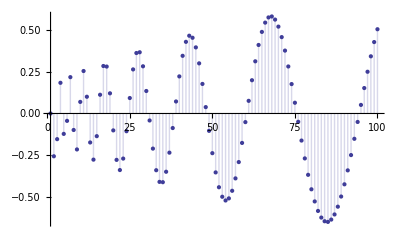

```mathematica
DiscretePlot[bb[n,-.5, Im@ZetaZero@1],{n,1,100}]
```

```mathematica
N[n^(-1-s-ⅈ t) (1+s+ⅈ t)j^(s+t I)-n^(-1-s+ⅈ t) (1+s-ⅈ t)j^(s-t I)/.j->7/.s->3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s (n^(-ⅈ t) (1+s+ⅈ t)j^(t I)-n^(ⅈ t) (1+s-ⅈ t)j^(-t I))/.j->7/.s->3/.t->4/.n->30]
```

-1.88053×10^-19+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s ((n/j)^(-ⅈ t) (1+s+ⅈ t)-(n/j)^(ⅈ t) (1+s-ⅈ t))/.j->7/.s->3/.t->4/.n->30]
```

-1.88053×10^-19+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s ((n/j)^(-ⅈ t) (1+s)-(n/j)^(ⅈ t) (1+s)+(n/j)^(-ⅈ t) (ⅈ t)-(n/j)^(ⅈ t) (-ⅈ t))/.j->7/.s->3/.t->4/.n->30]
```

-1.88053×10^-19+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s ((1+s)((n/j)^(-ⅈ t) -(n/j)^(ⅈ t) )+(ⅈ t)((n/j)^(-ⅈ t) +(n/j)^(ⅈ t)))/.j->7/.s->3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s ((1+s)(E^(-ⅈ Log[n/j]t) -E^(ⅈ Log[n/j] t) )+(ⅈ t)(E^(-ⅈ Log[n/j]t) +E^(ⅈ Log[n/j] t)))/.j->7/.s->3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
N[n^(-1-s)j^s (-(1+s)2I Sin[Log[n/j]t]+(ⅈ t)2 Cos[Log[n/j]t])/.j->7/.s->3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
N[n^-1 (n/j)^(-s) 2 I (t Cos[Log[n/j]t]-(1+s)Sin[Log[n/j]t])/.j->7/.s->3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
N[n^-1 (n/j)^(s) 2 I (t Cos[Log[n/j]t]-(1-s)Sin[Log[n/j]t])/.j->7/.s->-3/.t->4/.n->30]
```

0.+0.00454257 ⅈ

```mathematica
bl[n_,s_,t_]:= 2 I n^s Sum[ j^-s (t Cos[Log[n/j]t]-(1-s)Sin[Log[n/j]t]),{j,1,n}]
bl2[n_,A_,f_]:= n^(A+1/2) ∑_(j=1)^n j^(-1/2-A) (f Cos[f Log[n/j]]-(1/2-A) Sin[f Log[n/j]])
```

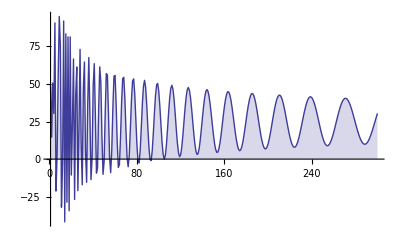

```mathematica
DiscretePlot[{bl2[n,-1,N@Im@ZetaZero@10]},{n,1,300}]
```

```mathematica
bl[100,-2,0]
```

0

```mathematica
2 I n^s Sum[ j^-s (t Cos[Log[n/j]t]-(1-s)Sin[Log[n/j]t]),{j,1,n}]/.t->f/.s->A+1/2
```

2 ⅈ n^(1/2+A) ∑_(j=1)^n j^(-1/2-A) (f Cos[f Log[n/j]]-(1/2-A) Sin[f Log[n/j]])

```mathematica
h1[n_,x_]:=(-1/2-x)n^-x HarmonicNumber[n,1/2-x]-(-1/2+x)n^x HarmonicNumber[n,1/2+x]
h2[n_,x_]:=(-1/3-x)n^-x HarmonicNumber[n,1/3-x]-(-1/3+x)n^x HarmonicNumber[n,1/3+x]
h3[n_,s_,t_]:=((1-s)n^s HarmonicNumber[n,s]-(1-t)n^t HarmonicNumber[n,t])/((1-s)n^s-(1-t)n^t)
h3a[n_,s_,t_]:=((1-t)n^t HarmonicNumber[n,t]-n)/((1-t)n^t-1)
h3b[n_,s_,t_]:=((1-t)n^t HarmonicNumber[n,t]-n)
```

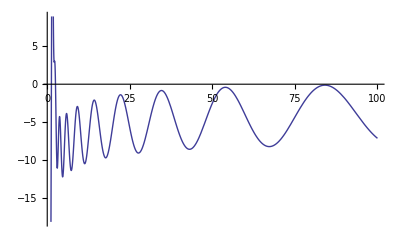

```mathematica
Plot[Im@h2[n,N@Im@ZetaZero@1 I],{n,1,100}]
```

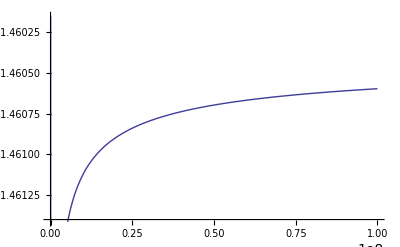

```mathematica
Plot[Re@h3a[n,-2, .5],{n,1,100000000}]
```

```mathematica
N@Zeta[.5]
```

-1.46035

```mathematica
((1-s)n^s HarmonicNumber[n,s]-(1-t)n^t HarmonicNumber[n,t])/((1-s)n^s-(1-t)n^t)/.s->0
```

(n-n^t (1-t) HarmonicNumber[n,t])/(1-n^t (1-t))

```mathematica
(1-(1-t)n^(t-1) HarmonicNumber[n,t])/(1/n-(1-t)n^(t-1))
```

```mathematica
Expand@((1-n^(-1+t) (1-t) HarmonicNumber[n,t])/(1/n-n^(-1+t) (1-t)))
```

1/(1/n-n^(-1+t) (1-t))-(n^(-1+t) HarmonicNumber[n,t])/(1/n-n^(-1+t) (1-t))+(n^(-1+t) t HarmonicNumber[n,t])/(1/n-n^(-1+t) (1-t))

```mathematica
FullSimplify@(1/(1/n-n^(-1+t) (1-t)))
```

n/(1+n^t (-1+t))

```mathematica
FullSimplify[-(n^(-1+t) HarmonicNumber[n,t])/(1/n-n^(-1+t) (1-t))+(n^(-1+t) t HarmonicNumber[n,t])/(1/n-n^(-1+t) (1-t))]
```

(n^t (-1+t) HarmonicNumber[n,t])/(1+n^t (-1+t))

```mathematica
(n-(1-t)n^t HarmonicNumber[n,t])/(1-(1-t)n^t)/.t->1/2+10I
```

(n-(1/2-10 ⅈ) n^(1/2+10 ⅈ) HarmonicNumber[n,1/2+10 ⅈ])/(1-(1/2-10 ⅈ) n^(1/2+10 ⅈ))

```mathematica
Limit[(n-(1/2-10 ⅈ) n^(1/2+10 ⅈ) HarmonicNumber[n,1/2+10 ⅈ])/(1-(1/2-10 ⅈ) n^(1/2+10 ⅈ)),n->1000000000.]
```

1.54491-0.11533 ⅈ

```mathematica
Zeta[.5+10I]
```

1.5449-0.115336 ⅈ

```mathematica
((1-t)n^t HarmonicNumber[n,t]-n)/((1-t)n^t-1)/.t->s
```

(-n+n^s (1-s) HarmonicNumber[n,s])/(-1+n^s (1-s))

```mathematica
pil[n_,s_]:=Sum[(1-s)(n/j)^s-1,{j,1,n}]/((1-s)n^s-1)
```

```mathematica
pil[10000000,.5+10I]
```

1.54476-0.11523 ⅈ

```mathematica
hx[n_,t_]:=2((1-t)n^t HarmonicNumber[n,t]-n)
hx2[n_,t_]:=((1-t)n^(t-1) HarmonicNumber[n,t]-1)
h3f[n_,t_]:=((1-t)n^t HarmonicNumber[n,t]-n)/((1-t)n^t-1)
h3ff[n_,t_]:=((1-t)n^t HarmonicNumber[n,t]-n)/((1-t)n^t)
h3fa[n_,t_]:=(-n)/((1-t)n^t-1)
h3fax[n_,t_]:=(-n)/((1-t)n^t)
h3fb[n_,t_]:=((1-t)n^t HarmonicNumber[n,t])/((1-t)n^t-1)
hy[n_,t_]:=2((1-t)n^t Sum[j^-t,{j,1,n}]-n)
hy2[n_,s_]:=2Sum[(1-s)(n/j)^s-1,{j,1,n}]
gg[n_,s_]:=2Sum[(1+s)(j/n)^s-1,{j,1,n}]
ggd[n_,s_]:=2 ∑_(j=1)^n ((j/n)^s+(j/n)^s (1+s) Log[j/n])
ggt[n_,s_]:=2Table[(1+s)(j/n)^s-1,{j,1,n}]
gggd[n2_,s_]:=DiscretePlot[{Re@ggd[n,s],Im@ggd[n,s]},{n,1,n2}]
ggg2d[n2_,s_]:=DiscretePlot[Abs@ggd[n,s],{n,1,n2}]
ggg[n2_,s_]:=DiscretePlot[{Re@gg[n,s],Im@gg[n,s]},{n,1,n2}]
ggg2[n2_,s_]:=DiscretePlot[Abs@gg[n,s],{n,1,n2}]
gga[n_,s_]:=2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s)
dgga[n_,s_]:=2 (-1-n^(-1-s) s (1+s) HarmonicNumber[n,-s]-n^-s s (1+s) (-HarmonicNumber[n,1-s]+Zeta[1-s]))
ggga[n2_,s_]:=DiscretePlot[{Re@gga[n,s],Im@gga[n,s]},{n,1,n2}]
dggga[n2_,s_]:=DiscretePlot[{Re@dgga[n,s],Im@dgga[n,s]},{n,1,n2}]
ggg2a[n2_,s_]:=DiscretePlot[Abs@gga[n,s],{n,1,n2}]
dggg2a[n2_,s_]:=DiscretePlot[Abs@dgga[n,s],{n,1,n2}]
ggg2as[n2_,s_]:=Plot[Abs@gga[n,s],{n,1,n2}]
gggas[n2_,s_]:=Plot[{Re@gga[n,s],Im@gga[n,s]},{n,1,n2}]
```

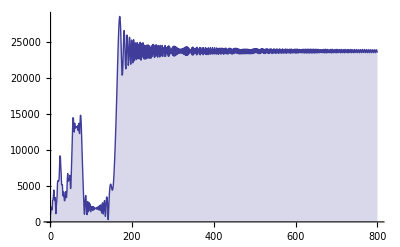

```mathematica
ggg2a[800,1000.I]
```

```mathematica
Abs[1+N@Im@ZetaZero@1000]
```

1420.42

```mathematica
Integrate[j^-s,{j,0,n}]^-1
```

ConditionalExpression[-n^(-1+s) (-1+s),Re[s]<1]

```mathematica
-N@ZetaZero@1000
```

-0.5-1419.42 ⅈ

```mathematica
Limit[gg[n,-1/10],n->Infinity]
```

-∞

```mathematica
Abs[(1+14.134725141734695I)+1]
```

14.2755

```mathematica
D[2Sum[(1+s)(j/n)^s-1,{j,1,n}],s]
```

2 ∑_(j=1)^n ((j/n)^s+(j/n)^s (1+s) Log[j/n])

```mathematica
FullSimplify@ggt[30,-1/2+Im@ZetaZero@1 I]
```

```mathematica
igg[n_,s_]:=2n((1+s)n^-(s+1)Sum[j^s,{j,1,n}]-1-(1+s)/(2n))
iagg[n_,s_]:=(2(1+s)n^-s Sum[j^s,{j,1,n}]-2n-(1+s))
igge[n_,s_]:=Sum[j^s,{j,1,n}]-n^(1+s)/(1+s)-n^s/2 
iggg[n2_,s_]:=DiscretePlot[{Re@igge[n,s],Im@igge[n,s]},{n,1,n2}]
```

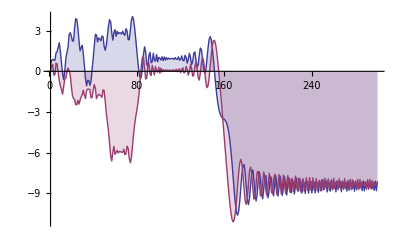

```mathematica
iggg[300,1000.I]
```

```mathematica
720/12
```

60

```mathematica
(BernoulliB[4]/4!)
```

-1/720

```mathematica
(BernoulliB[2]/2!)/(BernoulliB[4]/4!)
```

-60

```mathematica
(BernoulliB[4]/4!)/(BernoulliB[6]/6!)
```

-42

```mathematica
Table[Limit[D[x/(E^x-1),{x,k}]/k!,x->0]D[n^s,{n,k-1}],{k,1,9}]//TableForm
```

-n^s/2
1/12 n^(-1+s) s
0
-1/720 n^(-3+s) (-2+s) (-1+s) s
0
(n^(-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s)/30240
0
-(n^(-7+s) (-6+s) (-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s)/1209600
0

```mathematica
Table[Limit[D[x/(E^x-1),{x,k}]/k!,x->0],{k,0,5}]
```

{1,-1/2,1/12,0,-1/720,0}

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Table[bin[s,k]BernoulliB[k+1]n^(s-k)/(k+1),{k,0,5}]//TableForm
```

-n^s/2
1/12 n^(-1+s) s
0
-1/720 n^(-3+s) (-2+s) (-1+s) s
0
(n^(-5+s) (-4+s) (-3+s) (-2+s) (-1+s) s)/30240

```mathematica
D[2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s),n]
```

2 (-1-n^(-1-s) s (1+s) HarmonicNumber[n,-s]-n^-s s (1+s) (-HarmonicNumber[n,1-s]+Zeta[1-s]))

```mathematica
2(1+s)n^-s j^s-2n-(1+s)
```

-1-s+2 (-n+j^s n^-s (1+s))

```mathematica
2(1+s)n^-s j^s-2n-(1+s)/.s->A+f I
```

-1-A-ⅈ f-2 n+2 (1+A+ⅈ f) j^(A+ⅈ f) n^(-A-ⅈ f)

```mathematica
FullSimplify[ComplexExpand[Re[-1-A-ⅈ f-2 n+2 (1+A+ⅈ f) j^(A+ⅈ f) n^(-A-ⅈ f)]],{Element[j,Integers],Element[n,Integers]}]/.Arg[n]->0/.Arg[j]->0/.Abs[n]->n/.Abs[j]->j
```

n^-A (-n^A (1+A+2 n)+2 j^A ((1+A) Cos[1/2 f Log[j^2/n^2]]-f Sin[1/2 f Log[j^2/n^2]]))

```mathematica
n^-A (-n^A (1+A+2 n)+2 j^A ((1+A) Cos[f Log[j/n]]-f Sin[ f Log[j/n]]))
```

```mathematica
(- (1+A+2 n)+n^-A 2 j^A ((1+A) Cos[f Log[j/n]]-f Sin[ f Log[j/n]]))
```

-1-A-2 n+2 j^A n^-A ((1+A) Cos[f Log[j/n]]-f Sin[f Log[j/n]])

```mathematica
FullSimplify[ComplexExpand[Re[-1-A-ⅈ f+2 (-n+(1+A+ⅈ f) n^(-A-ⅈ f) HarmonicNumber[n,-A-ⅈ f])]],{Element[j,Integers],Element[n,Integers]}]/.Arg[n]->0/.Arg[j]->0/.Abs[n]->n/.Abs[j]->j
```

n^-A (-n^A (1+A+2 n)+(1/Sign[n])^(-ⅈ f) (2 (1+A-ⅈ f) n^(ⅈ f) Re[HarmonicNumber[n,-A-ⅈ f]] Sign[n]^A+2 ⅈ HarmonicNumber[n,-A-ⅈ f] (f Cos[1/2 f Log[n^2]]-(1+A) Sin[1/2 f Log[n^2]-ⅈ A Log[Sign[n]]])))

```mathematica
2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s)/.s->A+f I
```

-1-A-ⅈ f+2 (-n+(1+A+ⅈ f) n^(-A-ⅈ f) HarmonicNumber[n,-A-ⅈ f])

```mathematica
CForm[FullSimplify[ComplexExpand[Re[-1-A-ⅈ f-2 n+2 (1+A+ⅈ f)  n^(-A-ⅈ f)]],{Element[j,Integers],Element[n,Integers]}]/.Arg[n]->0/.Arg[j]->0/.Abs[n]->n/.Abs[j]->j]
```

(-(Power(n,A)*(1 + A + 2*n)) + 2*((1 + A)*Cos((f*Log(Power(n,2)))/2.) + f*Sin((f*Log(Power(n,2)))/2.)))/Power(n,A)

```mathematica
( (1+A+2 n)+2 n^-A((1+A) Cos[1/2 f Log[n^2]]+f Sin[1/2 f Log[n^2]]))
```

1+A+2 n+2 n^-A ((1+A) Cos[1/2 f Log[n^2]]+f Sin[1/2 f Log[n^2]])

```mathematica
CForm[FullSimplify[ComplexExpand[Im[-1-A-ⅈ f-2 n+2 (1+A+ⅈ f)  n^(-A-ⅈ f)]],{Element[j,Integers],Element[n,Integers]}]/.Arg[n]->0/.Arg[j]->0/.Abs[n]->n/.Abs[j]->j]
```

(-(f*Power(n,A)) + 2*(f*Cos((f*Log(Power(n,2)))/2.) - (1 + A)*Sin((f*Log(Power(n,2)))/2.)))/Power(n,A)

```mathematica
(-f +2 n^-A(f Cos[1/2 f Log[n^2]]-(1+A) Sin[1/2 f Log[n^2]]))
```

-f+2 n^-A (f Cos[1/2 f Log[n^2]]-(1+A) Sin[1/2 f Log[n^2]])

```mathematica
1+A+2 n+2 n^-A ((1+A) Cos[f Log[n]]+f Sin[f Log[n]])
```

1+A+2 n+2 n^-A ((1+A) Cos[f Log[n]]+f Sin[f Log[n]])

```mathematica
-f+2 n^-A (f Cos[ f Log[n]]-(1+A) Sin[ f Log[n]])
```

-f+2 n^-A (f Cos[f Log[n]]-(1+A) Sin[f Log[n]])

```mathematica
CForm[1+A+2 n+2 n^-A ((1+A) Cos[f Log[n]]+f Sin[f Log[n]])]
```

1 + A + 2*n + (2*((1 + A)*Cos(f*Log(n)) + f*Sin(f*Log(n))))/Power(n,A)

```mathematica
CForm[-f+2 n^-A (f Cos[f Log[n]]-(1+A) Sin[f Log[n]])]
```

-f + (2*(f*Cos(f*Log(n)) - (1 + A)*Sin(f*Log(n))))/Power(n,A)

```mathematica
plo[n_,A_,f_]:=(1+A+2 n+2 n^-A ((1+A) Cos[f Log[n]]+f Sin[f Log[n]]))Sum[j^A
```

```mathematica
Expand[2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s)/.s->A+f I]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
Expand[2((1+s)n^-s Sum[j^s,{j,1,n}]-n)-(1+s)/.s->A+f I]
```

-1-A-ⅈ f-2 n+2 n^(-A-ⅈ f) HarmonicNumber[n,-A-ⅈ f]+2 A n^(-A-ⅈ f) HarmonicNumber[n,-A-ⅈ f]+2 ⅈ f n^(-A-ⅈ f) HarmonicNumber[n,-A-ⅈ f]

```mathematica
2((1+A+f I)n^-(A+f I) Sum[j^A (Cos[f Log[j]]+I Sin[f Log[j]]),{j,1,n}]-n)-(1+A+f I)/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
2((1+A+f I)n^-(A+f I)( Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  Sum[j^A ( Sin[f Log[j]]),{j,1,n}])-n)-(1+A+f I)/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-f I-2n+2((1+A)+f I)n^-A E^(-f Log[n] I)( Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  Sum[j^A ( Sin[f Log[j]]),{j,1,n}])/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-f I-2n+2((1+A)+f I)n^-A (Cos[f Log[n]]-I Sin[f Log[n]])( Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  Sum[j^A ( Sin[f Log[j]]),{j,1,n}])/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-f I-2n+ 2((1+A)+f I)n^-A (Cos[f Log[n]]-I Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  2((1+A)+f I)n^-A (Cos[f Log[n]]-I Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-f I-2n+ 2n^-A (((1+A)+f I)Cos[f Log[n]]-I ((1+A)+f I)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  2n^-A (((1+A)+f I)Cos[f Log[n]]-I ((1+A)+f I)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-f I-2n+ 2n^-A (((1+A))Cos[f Log[n]]-I (f I)Sin[f Log[n]]+(f I)Cos[f Log[n]]-I ((1+A))Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  2n^-A (((1+A))Cos[f Log[n]]-I (f I)Sin[f Log[n]]+(f I)Cos[f Log[n]]-I ((1+A))Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n-f I+
2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]]+I(f Cos[f Log[n]]- (1+A)Sin[f Log[n]]))Sum[j^A (Cos[f Log[j]]),{j,1,n}]+I  2n^-A (((1+A))Cos[f Log[n]]+f Sin[f Log[n]]+I(f Cos[f Log[n]]-(1+A)Sin[f Log[n]]))Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n-f I+
2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
2n^-A (I(f Cos[f Log[n]]- (1+A)Sin[f Log[n]]))Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
I  2n^-A (((1+A))Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]+I  2n^-A (I(f Cos[f Log[n]]-(1+A)Sin[f Log[n]]))Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n-f I+
2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
I 2n^-A (f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
I  2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]+
- 2n^-A (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n+
2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
- 2n^-A (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]+
-f I+
I 2n^-A (f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
I  2n^-A ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n+
2n^-A( ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
- (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}])+
I(-f+
2n^-A ((f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
 ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]))/.n->10/.A->.5/.f->10
```

-13.6572-4.89332 ⅈ

```mathematica
-(1+A)-2n+
2n^-A( ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
- (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}])+
I(-f+
2n^-A ((f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
 ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]))/.Sum[j^A (Cos[f Log[j]]),{j,1,n}]->CosSum/.Sum[j^A ( Sin[f Log[j]]),{j,1,n}]->SinSum
```

-1-A-2 n+2 n^-A (SinSum (-f Cos[f Log[n]]+(1+A) Sin[f Log[n]])+CosSum ((1+A) Cos[f Log[n]]+f Sin[f Log[n]]))+ⅈ (-f+2 n^-A (CosSum (f Cos[f Log[n]]-(1+A) Sin[f Log[n]])+SinSum ((1+A) Cos[f Log[n]]+f Sin[f Log[n]])))

```mathematica
CForm[-1-A-2 n+2 n^-A (SinSum (-f Cos[f Log[n]]+(1+A) Sin[f Log[n]])+CosSum ((1+A) Cos[f Log[n]]+f Sin[f Log[n]]))]
```

-1 - A - 2*n + (2*(SinSum*(-(f*Cos(f*Log(n))) + (1 + A)*Sin(f*Log(n))) + CosSum*((1 + A)*Cos(f*Log(n)) + f*Sin(f*Log(n)))))/Power(n,A)

```mathematica
CForm[-f+2 n^-A (CosSum (f Cos[f Log[n]]-(1+A) Sin[f Log[n]])+SinSum ((1+A) Cos[f Log[n]]+f Sin[f Log[n]]))]
```

-f + (2*(CosSum*(f*Cos(f*Log(n)) - (1 + A)*Sin(f*Log(n))) + SinSum*((1 + A)*Cos(f*Log(n)) + f*Sin(f*Log(n)))))/Power(n,A)

```mathematica
N@ZetaZero@100000
```

```mathematica
0.5+74920.82749899419 ⅈ
```

0.5+74920.8 ⅈ

```mathematica
0.5+1419.4224809459956 ⅈ
```

0.5+1419.42 ⅈ

```mathematica
0.5+9877.782654005501 ⅈ
```

0.5+9877.78 ⅈ

```mathematica
-(1+A)-2n+
2n^-A( ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
- (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}])+
I(-f+
2n^-A ((f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
 ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]))
```

```mathematica
-1-A-2 n+2 n^-A (((1+A) Cos[f Log[n]]+f Sin[f Log[n]]) ∑_(j=1)^n j^A Cos[f Log[j]]+(-f Cos[f Log[n]]+(1+A) Sin[f Log[n]]) ∑_(j=1)^n j^A Sin[f Log[j]])+ⅈ (-f+2 n^-A ((f Cos[f Log[n]]-(1+A) Sin[f Log[n]]) ∑_(j=1)^n j^A Cos[f Log[j]]+((1+A) Cos[f Log[n]]+f Sin[f Log[n]]) ∑_(j=1)^n j^A Sin[f Log[j]]))/.n->E^(2 Pi n / f)/.Cos[f Log[ⅇ^((2 n π)/f)]]->1/.Sin[f Log[ⅇ^((2 n π)/f)]]->0
```

-1-A-2 ⅇ^((2 n π)/f)+2 (ⅇ^((2 n π)/f))^-A ((1+A) ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Cos[f Log[j]]-f ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Sin[f Log[j]])+ⅈ (-f+2 (ⅇ^((2 n π)/f))^-A (f ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Cos[f Log[j]]+(1+A) ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Sin[f Log[j]]))

```mathematica
Sin[f Log[ⅇ^((2 n π)/f)]]/.f->10/.n->4
```

0

```mathematica
-1-A-2 ⅇ^((2 n π)/f)+2 (ⅇ^((2 n π)/f))^-A ((1+A) ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Cos[f Log[j]]-f ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Sin[f Log[j]])+ⅈ (-f+2 (ⅇ^((2 n π)/f))^-A (f ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Cos[f Log[j]]+(1+A) ∑_(j=1)^(ⅇ^((2 n π)/f)) j^A Sin[f Log[j]]))/.A->-1/2
```

-1/2-2 ⅇ^((2 n π)/f)+ⅈ (-f+2 √(ⅇ^((2 n π)/f)) (f ∑_(j=1)^(ⅇ^((2 n π)/f)) Cos[f Log[j]]/(√j)+1/2 ∑_(j=1)^(ⅇ^((2 n π)/f)) Sin[f Log[j]]/(√j)))+2 √(ⅇ^((2 n π)/f)) (1/2 ∑_(j=1)^(ⅇ^((2 n π)/f)) Cos[f Log[j]]/(√j)-f ∑_(j=1)^(ⅇ^((2 n π)/f)) Sin[f Log[j]]/(√j))

```mathematica
CForm[-1/2-2 ⅇ^((2 n π)/f)+ √(ⅇ^((2 n π)/f)) ( CosSum-2f SinSum)]
```

-0.5 - 2*Power(E,(2*n*Pi)/f) + Sqrt(Power(E,(2*n*Pi)/f))*(CosSum - 2*f*SinSum)

```mathematica
CForm[-f+ √(ⅇ^((2 n π)/f)) (2 f CosSum+ SinSum)]
```

-f + Sqrt(Power(E,(2*n*Pi)/f))*(2*CosSum*f + SinSum)

```mathematica
FullSimplify[-f+2 √(ⅇ^((2 n π)/f)) (f CosSum+1/2 SinSum)]
```

-f+√(ⅇ^((2 n π)/f)) (2 CosSum f+SinSum)

```mathematica
FullSimplify[-1/2-2 ⅇ^((2 n π)/f)+2 √(ⅇ^((2 n π)/f)) (1/2 CosSum-f SinSum)]
```

-1/2-2 ⅇ^((2 n π)/f)+√(ⅇ^((2 n π)/f)) (CosSum-2 f SinSum)

```mathematica
N@Pi
```

```mathematica
3.141592653589793
```

```mathematica
N@E
```

```mathematica
2.718281828459045
```

```mathematica
CForm[ⅇ^((2 n π)/f)]
```

Power(E,(2*n*Pi)/f)

```mathematica
N@ZetaZero[10000000]/10
```

```mathematica
0.05+499238.10140031786 ⅈ
```

0.05+499238. ⅈ

```mathematica
0.5+4.992381014003178*^6 ⅈ
```

0.5+4.99238×10^6 ⅈ

```mathematica
0.5+600269.6770124449 ⅈ
```

0.5+600270. ⅈ

```mathematica
0.5+236.5242296658162 ⅈ
```

0.5+236.524 ⅈ

```mathematica
4.992381014003178`20*1000000
```

```mathematica
4.99238101400317799999999999999999999999973594`20.*^5
```

499238.1014003178

```mathematica
10^6
```

1000000

```mathematica
4992381.0140031786
```

```mathematica
2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s)/.n->100/.s->.5+10I
```

3.18945-2.37779 ⅈ

```mathematica
-(1+A)-2n+
2n^-A( ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
- (f Cos[f Log[n]]-(1+A)Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}])+
I(-f+
2n^-A ((f Cos[f Log[n]]- (1+A)Sin[f Log[n]])Sum[j^A (Cos[f Log[j]]),{j,1,n}]+
 ((1+A)Cos[f Log[n]]+f Sin[f Log[n]])Sum[j^A ( Sin[f Log[j]]),{j,1,n}]))/.n->100/.f->10./.A->.5
```

3.18945-2.37779 ⅈ

```mathematica
2n((1+s)n^(-s-1) HarmonicNumber[n,-s]-1)-(1+s)/.n->100/.s->.5+10I
```

3.18945-2.37779 ⅈ

```mathematica
FullSimplify[2n(1+s)n^(-s-1) (Sum[j^s,{j,1,n}]-Integrate[j^s,{j,0,n}])-(1+s)]
```

ConditionalExpression[-1-2 n-s+2 n^-s (1+s) HarmonicNumber[n,-s],Re[s]>-1]

```mathematica
10000000^.5
```

3162.28

```mathematica
CForm@Table[Prime[k],{k,1,PrimePi[3163]}]
```

List(2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,
   293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,
   641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,
   1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,
   1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,
   1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,
   1979,1987,1993,1997,1999,2003,2011,2017,2027,2029,2039,2053,2063,2069,2081,2083,2087,2089,2099,2111,2113,2129,2131,2137,2141,2143,2153,2161,2179,2203,2207,2213,2221,2237,2239,2243,2251,2267,2269,2273,2281,2287,2293,
   2297,2309,2311,2333,2339,2341,2347,2351,2357,2371,2377,2381,2383,2389,2393,2399,2411,2417,2423,2437,2441,2447,2459,2467,2473,2477,2503,2521,2531,2539,2543,2549,2551,2557,2579,2591,2593,2609,2617,2621,2633,2647,2657,
   2659,2663,2671,2677,2683,2687,2689,2693,2699,2707,2711,2713,2719,2729,2731,2741,2749,2753,2767,2777,2789,2791,2797,2801,2803,2819,2833,2837,2843,2851,2857,2861,2879,2887,2897,2903,2909,2917,2927,2939,2953,2957,2963,
   2969,2971,2999,3001,3011,3019,3023,3037,3041,3049,3061,3067,3079,3083,3089,3109,3119,3121,3137,3163)

```mathematica
Table[Factorial[k],{k,1,40}]
```

{1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000,51090942171709440000,1124000727777607680000,25852016738884976640000,620448401733239439360000,15511210043330985984000000,403291461126605635584000000,10888869450418352160768000000,304888344611713860501504000000,8841761993739701954543616000000,265252859812191058636308480000000,8222838654177922817725562880000000,263130836933693530167218012160000000,8683317618811886495518194401280000000,295232799039604140847618609643520000000,10333147966386144929666651337523200000000,371993326789901217467999448150835200000000,13763753091226345046315979581580902400000000,523022617466601111760007224100074291200000000,20397882081197443358640281739902897356800000000,815915283247897734345611269596115894272000000000}

```mathematica
LogIntegral[1000000.]
```

78627.5

```mathematica
N@Sum[PrimePi[100000^(1/k)]/k,{k,1,Log2@100000}]
```

9633.77

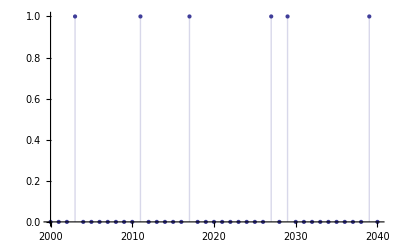

```mathematica
DiscretePlot[If[PrimeQ[j],1,0],{j,2000,2040}]
```

```mathematica
Log[10000000.]
```

16.1181

```mathematica
N@EulerGamma
```

0.577216

```mathematica
gga[n_,s_]:=2n((1+s)n^(-s-1) HarmonicNumber[n,-s]-1)-(1+s)
ggaa[n_,s_]:=gga[n,s]/(2n^-s(1+s))
gga1[n_,s_]:=(2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s))/(2n^-s(1+s))
gga2[n_,s_]:=HarmonicNumber[n,-s]-n^(1+s)/(1+s)+(n^s (-1-s))/(2 (1+s))
gga3[n_,s_]:=HarmonicNumber[n,-s]-n^(1+s)/(1+s)-n^s/2
```

```mathematica
gga[10000000000,-N@ZetaZero[1]]
```

-8.84041×10^-6+0.000161622 ⅈ

```mathematica
Zeta[-(.5+200I)]
```

32.8715+49.3787 ⅈ

```mathematica
(2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s))/(2n^-s(1+s))/.s->0
```

-1/2

```mathematica
FullSimplify[(2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s))/(2n^-s(1+s))]
```

-(n^s (1+2 n+s))/(2 (1+s))+HarmonicNumber[n,-s]

```mathematica
(2(-n))/(2n^-s(1+s))
```

-n^(1+s)/(1+s)

```mathematica
(-(1+s))/(2n^-s(1+s))
```

(n^s (-1-s))/(2 (1+s))

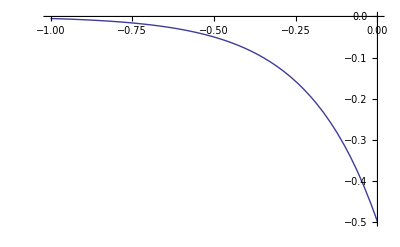

```mathematica
Plot[(n^s (-1-s))/(2 (1+s))/.n->100,{s,-1,0}]
```

```mathematica
HarmonicNumber[n,-s]-n^(1+s)/(1+s)+(n^s (-1-s))/(2 (1+s))/.s->-s
```

-n^(1-s)/(1-s)+(n^-s (-1+s))/(2 (1-s))+HarmonicNumber[n,s]

```mathematica
ggo[n_,s_]:=(1+s)-2n((1+s)n^(-s-1) HarmonicNumber[n,-s]-1)
```

```mathematica
Limit[ggo[n,I],n->Infinity]
```

Indeterminate

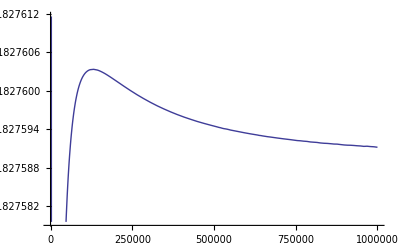

```mathematica
Plot[Abs[ggo[n, I]],{n,0,1000000}]
```

```mathematica
Limit[Abs[ggo[n,I]],n->Infinity]
```

$Aborted

```mathematica
N@E
```

2.71828

```mathematica
N@Log[Pi]
```

1.14473

```mathematica
gga1[n_,s_]:=((1+s)-2((1+s)n^-s HarmonicNumber[n,-s]-n))/(-2n^-s(1+s))
gga1a[n_,s_]:=1/(-2n^-s(1+s))
ggoo[n_,s_]:=((1+s)-2n((1+s)n^(-s-1) HarmonicNumber[n,-s]-1))
```

```mathematica
Limit[ggoo[n,-ZetaZero[1]],n->Infinity]
```

0

```mathematica
Zeta[-(.5+3I)]
```

0.352914-0.012125 ⅈ

```mathematica
gga1[100000,.5+3I]
```

0.352767-0.0129129 ⅈ

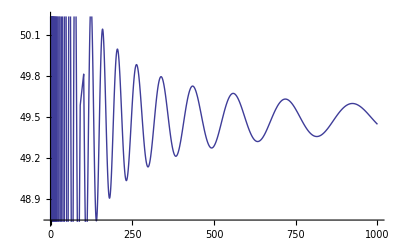

```mathematica
Plot[Abs[ggo[n,N@Im@ZetaZero@3 I]],{n,0,1000}]
```

```mathematica
hha1[n_,s_]:=(2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s))/(2n^-s(1+s))
hha1a[n_,s_]:=(2((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s))
hha2[n_,s_]:=(((1+s)n^-s HarmonicNumber[n,-s]-n)-(1+s)/2)/(n^-s(1+s))
hha3[n_,s_]:=(((1+s)n^(1-s) HarmonicNumber[n,-s]-n^2)-(1+s)n/2+(1+s)(-s)/12)/(n^(1-s)(1+s))
hha3a[n_,s_]:=(((1+s)n^(1-s) HarmonicNumber[n,-s]-n^2)-(1+s)n/2+(1+s)(-s)/12)
hha5[n_,s_]:=(((1+s)n^(1-s) HarmonicNumber[n,-s]-n^2)-(1+s)n/2+(1+s)(-s)/12-n^(-2)(1+s)(-s)(1-s)(2-s)/720)/(n^(1-s)(1+s))
hha5t[n_,s_]:=(((1+s)n^(3-s) HarmonicNumber[n,-s]-n^4)-(1+s)n^3/2+n^2(1+s)(-s)/12-(1+s)(-s)(1-s)(2-s)/720)/(n^(3-s)(1+s))
hha5a[n_,s_]:=(((1+s)n^(3-s) HarmonicNumber[n,-s]-n^4)-(1+s)n^3/2+n^2(1+s)(-s)/12-(1+s)(-s)(1-s)(2-s)/720)
hha5b[n_,s_]:=(1+s)((n^(3-s) HarmonicNumber[n,-s]-n^4/(1+s))-n^3/2+n^2(-s)/12-(-s)(1-s)(2-s)/720)
hha5c[n_,s_]:=(1+s)n^(3-s)( HarmonicNumber[n,-s]-n^(s+1)/(1+s)-n^s/2+n^(s-1)(-s)/12-n^(s-3)(-s)(1-s)(2-s)/720)
hha5d[n_,s_]:=(1+s)n^(5-s)( HarmonicNumber[n,-s]-n^(s+1)/(1+s)-n^s/2+n^(s-1)(-s)/12-n^(s-3)(-s)(1-s)(2-s)/720+n^(s-5)(-s)(1-s)(2-s)(3-s)(4-s)/30240)
```

```mathematica
hha5t[100,-N@ZetaZero@1]
```

-2.69918×10^-12+2.06203×10^-10 ⅈ

```mathematica
Zeta[-(.5+10I)]
```

2.04226+0.0497166 ⅈ

```mathematica
Limit[hha5c[n,-ZetaZero@1],n->Infinity]
```

0

```mathematica
FullSimplify[(((1+s)n^(3-s) HarmonicNumber[n,-s]-n^4)-(1+s)n^3/2+n^2(1+s)(-s)/12-(1+s)(-s)(1-s)(2-s)/720)]
```

-n^4-1/2 n^3 (1+s)-1/12 n^2 s (1+s)+1/720 (-2+s) (-1+s) s (1+s)+n^(3-s) (1+s) HarmonicNumber[n,-s]

```mathematica
(1+s)n^(3-s)(( HarmonicNumber[n,-s]-n^(s+1)/(1+s))-n^s/2+n^(s-1)(-s)/12-n^(s-3)(-s)(1-s)(2-s)/720)
```

```mathematica
BernoulliB[6]/6!
```

1/30240